# An Introduction to Mathematical Modeling in Ecology and Evolution Sally Otto (2020)

Sponsors:
BIOS2 (NSERC - CREATE Training program)

Resources:
* An Introduction to Mathematical Modeling in Ecology and Evolution (2007) by Otto and Day
* Biomathematical modeling lecture notes (http://www.zoology.ubc.ca/~bio301/Bio301/Lectures.html)
* Mathematica labs (http://www.zoology.ubc.ca/biomath/labs.htm)

## Part 1: Classic one-variable models in ecology and evolution

### Exponential growth

Assumes that each individual replicates at a constant rate over time:

	 n[t+1] = R n[t]						Discrete-time model ("Recursion equation")
	
	 dn/dt=n'[t]= r n[t]						Continuous-time model ("Differential equation")
	
n[t]:	The population size at time t 
R:	The number of offspring per parent in a time unit (from t to t+1).
r:	The growth rate per parent per time unit.

### Logistic growth

Assumes that each individual replicates at a rate that declines as a linear function of the current population size:

	 n[t+1] =(1+r (1-n[t]/K))n[t]				Discrete-time model
	
	dn/dt=n'[t]=r (1-n[t]/K) n[t]					Continuous-time model
	
r:  	The "intrinsic" growth rate per parent per unit time, realized when competition is weak (population size small)
K:  	The "carrying capacity" defined as the population size at which competition causes the population to neither grow nor shrink

### Haploid model of selection

Assumes that each individual carrying A has a fitness of 1+s relative to individuals carrying a, where p is the frequency of A:

	 p[t+1] =((1+s)p[t])/((1+s)p[t]+(1-p[t]))					Discrete-time model
	
	dp/dt=p'[t]=s p[t] (1-p[t])					Continuous-time model
	
p:	Frequency of allele A at a locus with two alleles (a and A).  p must lie between 0 and 1.
s:	Selection coefficient favoring allele A over a.

### Getting used to Mathematica

Mathematica can be used as a sophisticated calculator.

For example, if r = 0.3, K = 100, and n = 90 at some time, what population size do we expect in the next generation?

```mathematica
(1+r (1-n/K))n/.n->90/.r->0.3/.K->100
```

92.7

Mathematica can also plots functions.

For example, the per capita number of offspring per parent in the logistic model:

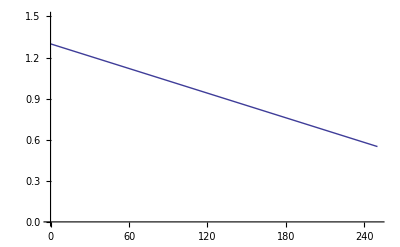

```mathematica
Plot[(1+r (1-n/K))/.r->0.3/.K->100,{n,0,250},PlotRange->{Automatic,{0,1.5}}]
```

```mathematica
Manipulate[Plot[(1+r (1-n/K)),{n,0,250},PlotRange->{Automatic,{0,1.5}}],{{r,0.3},0.01,0.5},{{K,100},10,200}]
```

Or the number of offspring produced by the entire population in the logistic model:

```mathematica
Manipulate[Plot[(1+r (1-n/K))*n,{n,0,250},PlotRange->{Automatic,{0,200}}],{{r,0.3},0.01,0.5},{{K,100},10,200}]
```

The real power of Mathematica, however, is that it can handle commands involving variables and parameters without having to specify their values.

For example, at what population size do we see the largest total number of offspring produced in the logistic model?

```mathematica
D[(1+r (1-n/K))n,n]
```

1-(n r)/K+(1-n/K) r

```mathematica
Solve[%==0,n]
```

{{n→(K (1+r))/(2 r)}}

This checks against the graph above

```mathematica
%/.r->0.3/.K->100
```

{{n→216.667}}

#### Question 1: At what speed does an allele rise in frequency?

Using the continuous-time model, plot the rate of change  s p(1-p)as a function of p (between 0 and 1).  Choose whatever numerical value of s you wish.

#### Question 2: When is evolutionary change fastest?

Again, using the continuous-time model, dp/dt=s p[t] (1-p[t]), what value of p maximizes the rate of allele frequency change?  Use D[] to find this result analytically, for any possible value of s.

```mathematica
D[s p (1-p),p]
```

(1-p) s-p s

```mathematica
Solve[%==0,p]
```

{{p→1/2}}

## Part 2: Equilibria and their stability

### Equilibria

DEFINITION:  An equilibrium is a special value of a variable such that if a system starts at that value, it stays there.

RECIPE: We find equilibria by:
	* Setting the variable at one time and the next (n[t + 1] and n[t]) to the same equilibrium value, n̂,	(Discrete-time model)
	* Setting the change in a variable (dn/dt) to zero when started at n̂,					(Continuous-time model)
and then solving for the value(s) of n̂ that satisfy the resulting equations.

E.g., in the logistic model, if the population size at time t is n[t]=n̂, it will remain at this value only if n[t+1]=n̂, which gives us an equation that we can solve for n̂, by replacing all instances of n with n̂ in  n[t+1] =(1+r (1-n[t]/K))n[t].

```mathematica
Solve[n̂ ==(1+r (1-(n̂)/K))n̂,n̂]
```

{{n̂→0},{n̂→K}}

NOTE:  We use == instead of = here because we don't want to set n̂ equal to the right-hand side, we want TO TEST when the left and right will be equal.

Similarly, in continuous-time, we determine what value of n̂ causes  dn/dt= r (1-n[t]/K) n[t] to equal zero:

```mathematica
Solve[0==r (1-(n̂)/K)n̂,n̂]
```

{{n̂→0},{n̂→K}}

#### Question 3: What are the equilibria for the haploid model of selection?

Find p̂ for both the discrete-time and continuous-time models:

	 p[t+1] =((1+s)p[t])/((1+s)p[t]+(1-p[t]))					Discrete-time model
	
	dp/dt=p'[t]=s p[t] (1-p[t])					Continuous-time model
	
First, use Mathematica to solve for p̂ analytically.
Second, carry out the calculations by hand.

For the recursion equation:

```mathematica
Solve[p̂==((1+s)p̂)/((1+s)p̂+(1-p̂)),p̂]
```

{{p̂→0},{p̂→1}}

By hand:
	p̂==((1+s)p̂)/((1+s)p̂+(1-p̂))		Divide both sides by p̂, noting when you do that this factor can be set to zero to give an equilibrium at p̂=0
	1==((1+s)1)/((1+s)p̂+(1-p̂))		Multiply out the denominator
	(1+s)p̂+(1-p̂)==(1+s)		Expand and cancel terms
	s p̂==s			Divide through by s to find  another equilibrium at p̂=0

For the differential equation:

```mathematica
Solve[s p̂(1-p̂)==0,p̂]
```

{{p̂→0},{p̂→1}}

By hand:
	s p̂(1-p̂)==0		As this equation is already factored, there are three ways for it to be solved. 
					(a) s = 0, which is not an equilibrium but a special case of the parameters.
					(b) p̂=0, an equilibrium
					(c) p̂=1, another equilibrium

### Stability

A system may or may not move toward a particular equilibrium.

DEFINITION:  An equilibrium is locally stable if a system near the equilibrium approaches it (attracting).  An equilibrium is unstable if a system near the equilibrium moves away from it (repelling).

A local stability analysis determines whether a system that starts near an equilibrium moves toward (stable) or away from it (unstable).

The idea:  We approximate the dynamics of a model near an equilibrium and then determine how it moves.  To do so, we use an incredibly useful approximation tool:  the Taylor Series.

Taylor series:  For any nicely behaved function, f, of a variable, x[t], we can write the function around x̂ as a series of terms, (x[t]-x̂)^i:

```mathematica
Series[f[x[t]],{x[t],x̂,4 }]
```

f[x̂]+f'[x̂] (x[t]-x̂)+1/2 f''[x̂] (x[t]-x̂)^2+1/6 f^(3)[x̂] (x[t]-x̂)^3+1/24 f^(4)[x̂] (x[t]-x̂)^4+O[x[t]-x̂]^5

For example, Sin[x] can be rewritten as the following function around the point 1/2:

```mathematica
Series[Sin[x],{x,1/2,4}]
```

Sin[1/2]+Cos[1/2] (x-1/2)-1/2 Sin[1/2] (x-1/2)^2-1/6 Cos[1/2] (x-1/2)^3+1/24 Sin[1/2] (x-1/2)^4+O[x-1/2]^5

If we are close enough to the point of interest, then (x[t]-x̂)^i will be small, and we can drop terms that we consider to be negligible.

Constant approximation (drops (x[t]-x̂)^i for i > 0):

```mathematica
const=Normal[Series[Sin[x],{x,1/2,0}]]
```

Sin[1/2]

Linear approximation (drops (x[t]-x̂)^i for i > 1):

```mathematica
lin=Normal[Series[Sin[x],{x,1/2,1}]]
```

(-1/2+x) Cos[1/2]+Sin[1/2]

Quadratic approximation (drops (x[t]-x̂)^i for i > 2):

```mathematica
quad=Normal[Series[Sin[x],{x,1/2,2}]]
```

(-1/2+x) Cos[1/2]+Sin[1/2]-1/2 (-1/2+x)^2 Sin[1/2]

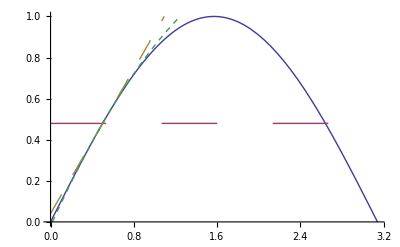

```mathematica
Plot[{Sin[x],const,lin, quad},{x,0,Pi},PlotRange->{Automatic,{0,1}},PlotStyle->{Automatic,Dashing[0.1],Dashing[0.04],Dashing[0.01]}]
```

In a local stability analysis, we assume that we are near an equilibrium, and use the Taylor series to approximate the recursion or differential equation, f[n], to linear order:

```mathematica
Normal[Series[f[n[t]],{n[t],n̂ ,1}]]
```

Describing the recursion equation as a function (f), where n[t+1]=f[n[t]], the Taylor series tells us that:

	n[t+1]≈f[n̂]+(n[t]-n̂) f'[n̂]	(note that f'[n̂] is the derivative of f with respect to n, evaluated at n̂: (df/dn)_(n=n̂))
	n[t+1]≈n̂ +(n[t]-n̂) f'[n̂]	(f[n̂]=n̂ because the recursion started at an equilibrium returns the equilibrium)
	(n[t+1]-n̂)≈(n[t]-n̂) f'[n̂]	(moving n̂ to the left)

so the distance to the equilibrium (n[t]-n̂) changes by a factor λ=f'[n̂] each generation.

Describing the differential equation as a function (f), where dn/dt=f[n[t]], the Taylor series tells us that:

	dn/dt≈f[n̂]+(n[t]-n̂) f'[n̂]
	dn/dt≈0 +(n[t]-n̂) f'[n̂]		(f[n̂]=0 because there is no change at an equilibrium)
	(d(n[t]-n̂))/dt≈(n[t]-n̂) f'[n̂]		(because (d(n[t]-n̂))/dt=(d(n[t]))/dt-(d(n̂))/dt= (d(n[t]))/dt-0)

so the distance to the equilibrium changes at a rate r=f'[n̂].

RECIPE: To determine the stability of an equilibrium:
	* Take the derivative of the recursion equation with respect to the variable, df/dn, and evaluate at an equilibrium λ=(df/dn)_(n=n̂).
		→  The equilibrium is stable only if -1<λ<1						(Discrete-time model)
			If 1<λ, equilibrium is unstable with exponential growth away from it
			If 0<λ<1, equilibrium is stable with exponential growth toward it
			If -1<λ<0, equilibrium is stable with damped oscillations toward it
			If λ<-1, equilibrium is unstable with growing oscillations away from it
 	* Take the derivative of the differential equation with respect to the variable, df/dn, and evaluate at an equilibrium r=(df/dn)_(n=n̂).
		→  The equilibrium is stable only if r < 0						(Continuous-time model)
			If 0<r, equilibrium is unstable with exponential growth away from it
			If r<0, equilibrium is stable with exponential growth toward it

Repeat for each equilibrium of interest.

For example, consider the logistic model in discrete time.  When will the system approach n̂ = 0, causing the system to go extinct?

```mathematica
derivative=D[(1+r (1-n[t]/K))n[t],n[t]]
```

1-(r n[t])/K+r (1-n[t]/K)

```mathematica
λ=derivative/.n[t]->0
```

1+r

For λ to lie between -1 and +1, r must lie between -2 and 0.  [Technically, because 1+r measures the number of offspring per parent when comeptition is weak, r cannot fall below -1 or it becomes biologically meaningless.]

When will the system approach n̂ = K, causing the system to remain stably at carrying capacity?

```mathematica
λ=derivative/.n[t]->K
```

1-r

λ will be greater than one if:	r<0		n̂=K is an unstable equilibrium
λ will be between 0 and 1 if:	0<r<1		n̂=K is a stable equilibrium
λ will be between -1 and 0 if:	1<r<2		n̂=K is a stable equilibrium with damped oscillations
λ will be less than -1 if:	r>2		n̂=K is an unstable equilibrium with growing oscillations

#### Question 4: What determines stability of the equilibria for the haploid model of selection?

Under what conditions is p̂=0 stable? 

	 p[t+1] =((1+s)p[t])/((1+s)p[t]+(1-p[t]))					Discrete-time model
	
	dp/dt=p'[t]=s p[t] (1-p[t])					Continuous-time model

Under what conditions is p̂=1 stable?

You can use either the discrete-time or the continuous-time model:

	 p[t+1] =((1+s)p[t])/((1+s)p[t]+(1-p[t]))					Discrete-time model
	
	dp/dt=p'[t]=s p[t] (1-p[t])					Continuous-time model

Note that, in the discrete-time model, the fitness of A individuals is 1+s times greater than the fitness of a individuals, where 1+s must be positive (fitness can't be negative).

Discrete-time model:

```mathematica
derivative=D[((1+s)p[t])/((1+s)p[t]+(1-p[t])),p[t]]
```

-(s (1+s) p[t])/(1-p[t]+(1+s) p[t])^2+(1+s)/(1-p[t]+(1+s) p[t])

(You could use the quotient rule to rederive the above.)

```mathematica
λ=derivative/.p[t]->0
```

1+s

As 1+s must be positive (its a fitness), 
	λ will be greater than one if:	s>0		p̂=0 is an unstable equilibrium (because A is favored)
	λ will be between 0 and 1 if:	-1<s<0		p̂=0 is a stable equilibrium (because A is selected against)

```mathematica
λ=derivative/.p[t]->1
```

1-s/(1+s)

```mathematica
Factor[%]
```

1/(1+s)

As 1+s must be positive (its a fitness), 
	λ will be between 0 and 1 if:	s>0		p̂=1 is a stable equilibrium (because A is favored)
	λ will be greater than one if:	-1<s<0		p̂=1 is an unstable equilibrium (because A is selected against)

Continuous-time model:

```mathematica
derivative=D[s p[t](1-p[t]),p[t]]
```

s (1-p[t])-s p[t]

(You could use the quotient rule to rederive the above.)

```mathematica
λ=derivative/.p[t]->0
```

s

λ will be positive if:	s>0		p̂=0 is an unstable equilibrium (because A is favored)
	λ will be negative if:	s<0		p̂=0 is a stable equilibrium (because A is selected against)

```mathematica
λ=derivative/.p[t]->1
```

-s

λ will be negative if:	s>0		p̂=1 is a stable equilibrium (because A is favored)
	λ will be positive if:	s<0		p̂=1 is an unstable equilibrium (because A is selected against)

## Part 3: Beyond equilibria

### General solutions

Some models can be solved generally, allowing us to predict the future state at any time in the future and how this depends on the parameters.

DEFINITION:  A general solution describes the state of a system at any future point in time.

There are many methods for finding general solutions (see Chapters 6 & 9), including iterating recursions to deduce a general rule and using recipes to solve differential equations (e.g., separation of variables).

Mathematica makes it easy to find general solutions for many of the simpler models.

Recursion equations:

```mathematica
RSolve[{n[t+1] == R*n[t],n[0]==n0},n[t],t]
```

{{n[t]→n0 R^t}}

NOTE:  Again, we use == instead of = here because we don't want to set n[t+1] equal to the right-hand side, we want TO TEST when the left and right will be equal.

```mathematica
RSolve[{p[t+1] ==((1+s)p[t])/((1+s)p[t]+(1-p[t])),p[0]==p0},p[t],t]
```

{{p[t]→(p0 (1/(1+s))^-t)/(1-p0+p0 (1+s)^t)}}

Note that Mathematica doesn't simplify the fraction on top unless you specify that the denominator is positive:

```mathematica
Simplify[(1/(1+s))^-t,{1+s>0}]
```

(1+s)^t

Differential equations:

```mathematica
DSolve[{D[n[t],t] == R*n[t],n[0]==n0},n[t],t]
```

{{n[t]→ⅇ^(R t) n0}}

```mathematica
DSolve[{D[p[t],t] ==s p[t](1-p[t]),p[0]==p0},p[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p[t]→(ⅇ^(s t) p0)/(1-p0+ⅇ^(s t) p0)}}

These can then be used to predict where the system will be:

```mathematica
Manipulate[Plot[(ⅇ^(s t) p0)/(1-p0+ⅇ^(s t) p0),{t,0,100},PlotRange->{Automatic,{0,1}}],{{s,0.1},-0.2,0.2},{{p0,0.05},0.01,0.99}]
```

#### Question 5: Show that the logistic model in discrete time does not have a solution, but the model in continuous time does and and then plot this solution.

Use: 

	 n[t+1] =(1+r (1-n[t]/K))n[t]				Discrete-time model
	
	dn/dt=n'[t]=r (1-n[t]/K) n[t]					Continuous-time model

```mathematica
DSolve[{D[n[t],t] ==r (1-n[t]/K) n[t],n[0]==n0},n[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n[t]→(ⅇ^(r t) K n0)/(K-n0+ⅇ^(r t) n0)}}

Note that this has the same form as the solution for the haploid model, (ⅇ^(s t) p0)/(1-p0+ⅇ^(s t) p0), if we let K=1, n0=p0, and r=s.  This is only true for the continuous-time models, however, and the discrete-time models behave much differently.

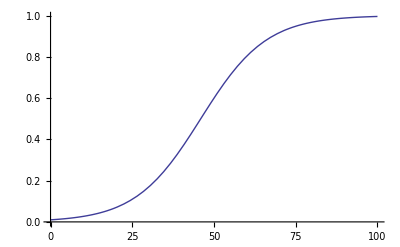

```mathematica
Plot[(ⅇ^(r t) K n0)/(K-n0+ⅇ^(r t) n0)/.s->0.1/.p0->0.01,{t,0,100}]
```

### Simulations

Some models, however, are too complicated to solve.  Some cannot be solved (e.g., the logistic in discrete time), while others may not be worth the time needed to obtain a general solution when all that is needed are solutions to specific cases.

DEFINITION:  A simulation explores a model using specific parameter values and initial states by applying the model's equations repeatedly.

```mathematica
Clear[logistic]
logistic[r_,K_,n0_,t_]:=logistic[r,K,n0,t]=
Block[{n=logistic[r,K,n0,t-1]},
	n+r n (1-n/K)
	]

logistic[r_,K_,n0_,0]:=n0
```

Some notes:  
	* Block keeps a set of calculations together, defining local variables in the first {}.  The output will be the last entry of the Block.
	* := sets the left to the right-hand side only after being called and remembers this value.
	* We have to set a starting point or else the system will end up in an infinite loop going backwards in time.

We can then make a table of population sizes:

```mathematica
Table[logistic[1.9,100,10,t],{t,0,100}]
```

{10,27.1,64.6362,108.066,91.5044,106.275,93.6047,104.979,95.0482,103.991,96.1058,103.217,96.9084,102.601,97.5307,102.107,98.0198,101.708,98.4077,101.385,98.7172,101.123,98.9651,100.911,99.1643,100.739,99.3246,100.599,99.4539,100.486,99.5583,100.394,99.6426,100.319,99.7108,100.259,99.7659,100.21,99.8105,100.17,99.8465,100.138,99.8757,100.112,99.8994,100.09,99.9185,100.073,99.934,100.059,99.9466,100.048,99.9567,100.039,99.9649,100.032,99.9716,100.026,99.977,100.021,99.9814,100.017,99.9849,100.014,99.9878,100.011,99.9901,100.009,99.992,100.007,99.9935,100.006,99.9947,100.005,99.9957,100.004,99.9965,100.003,99.9972,100.003,99.9977,100.002,99.9982,100.002,99.9985,100.001,99.9988,100.001,99.999,100.001,99.9992,100.001,99.9994,100.001,99.9995,100.,99.9996,100.,99.9997,100.,99.9997}

and plot this list:

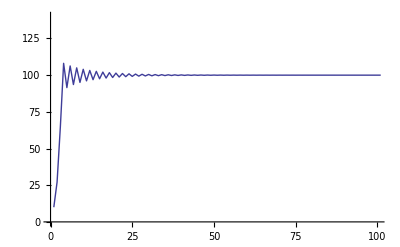

```mathematica
ListPlot[Table[logistic[1.9,100,10,t],{t,0,100}],PlotRange->{{0,100},{0,140}},Joined->True]
```

For r values between 0 and 2, we see a stable equilibrium, as we would expect from the local stability analysis of n̂=k.  For 2<r, we see oscillations, for 2.58<r, chaotic dynamics are observed, while for 3<r the system is driven extinct.

Notice, though, that the oscillations get so large when 3<r, that the system can no longer calculate the next population size:

```mathematica
Table[logistic[3.01,100,10,t],{t,0,100}]
```

{10,37.09,107.323,83.6659,124.801,31.6366,96.7364,106.239,86.2876,121.902,41.5373,114.632,64.1465,133.373,-0.602954,-2.42879,-9.91701,-42.7274,-226.289,-2448.73,-190308.,-1.0909×10^9,-3.58209×10^16,-3.86223×10^31,-4.48997×10^61,-6.06812×10^121,-1.10834×10^242,-3.69756324465319×10^482,-4.11526415841128×10^963,-5.09755512714486×10^1925,-7.82150555055852×10^3849,-1.84139606723027×10^7698,-1.02061258239975×10^15395,-3.13536663049157×10^30788,-2.95898769618763×10^61575,-2.63543806404312×10^123149,-2.0906056706116×10^246297,-1.315560253068×10^492593,-5.2094033261516×10^985184,-8.1685027873704×10^1970367,-2.0084055773971×10^3940734,-1.2141415819592×10^7881467,-4.4371607409378×10^15762932,-5.9262070277169×10^31525863,-1.0571098850344×10^63051726,-3.3636187402026×10^126103450,-3.405493239862×10^252206899,Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[]}

#### Question 6: Simulating extinction

Add an If[ ] statement to the above simulation to return zero if ever the population size is predicted to be negative.

Use this simulation to explore what happens with r = 3.01 (generate a table as above, and ListPlot it).

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
Clear[logistic]

logistic[r_,K_,n0_,t_]:=logistic[r,K,n0,t]=
Block[{n=logistic[r,K,n0,t-1]},
	If[(newn=n+r n (1-n/K))>0,newn,0]
	]

logistic[r_,K_,n0_,0]=n0
```

n0

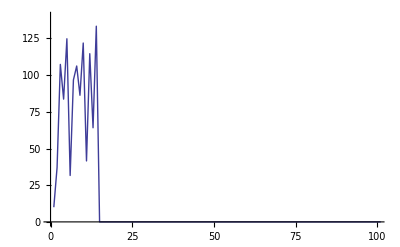

```mathematica
ListPlot[Table[logistic[3.01,100,10,t],{t,0,100}],PlotRange->{{0,100},{0,140}},Joined->True]
```

### Numerical solutions

Differential equations can also be solved numerically using Mathematica's NDSolve routines, which can work even for models that cannot be solved analytically.

```mathematica
logisticD[r_,K_,n0_]:=NDSolve[{D[n[t],t]==r (1-n[t]/K) n[t],n[0]==n0},n[t],{t,0,100}]
```

```mathematica
logisticD[0.5,100,10]
```

{{n[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

Some notes:  
	* We must use := here because we don't want the routine to start calculating until we call it with specific values of the parameters.
	* The code is very similar to DSolve, except that we must specify the time frame over which we want a solution (here 0-100)
	* When we do call the function, Mathematica tells us that it has represented the solution as a function, which we can interrogate.

We can then evaluate this function at specific values or in a plot:

```mathematica
logisticD[0.1,100,10]/.t->20
```

{{n[20]→45.0853}}

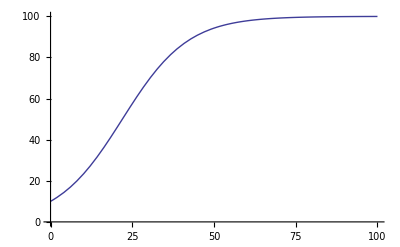

```mathematica
Plot[Evaluate[n[t]/.logisticD[0.1,100,10]],{t,0,100}]
```

## Part 4: Example of building a model from scratch

Scenario:  Let's model the number of species on a large landmass over long periods of evolutionary time, where the number of species is primarily influenced by speciation and extinction events within the landmass.  If extinction risk, d, is constant per species but speciation rate declines from an initial value, b, exponentially with the number of species already present (because of competition for overlapping resources/niches), then develop a model that might describe the number of species, n, on the landmass.

### Discrete-time approach

n[t + 1] = n[t] - d n[t] + b n[t] Exp[-a n[t]]

```mathematica
Solve[nhat==nhat-d nhat + b Exp[-a nhat] nhat,nhat]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{nhat→0},{nhat→Log[b/d]/a}}

Here, I've used nhat to stand for the equilibrium.  The first equilibrium to consider is the no-species case.  The second equilibrium is biologically valid only if it is not negative, which requires that b>d.

The first equilibrium (no-species case) will be unstable if λ>1, which the following shows requires that b>d, that is, if speciation is more common than extinction when there are few species present:

```mathematica
λ=D[n[t]-d n[t]+b n[t] Exp[-a n[t]],n[t]]/.n[t]->0
```

1+b-d

Now considering the second equilibrium:

```mathematica
λ=D[n[t]-d n[t]+b n[t] Exp[-a n[t]],n[t]]/.n[t]->Log[b/d]/a
```

1-d Log[b/d]

As this second equilibrium is only biologically valid when b>d, we know that λ must be less than one:
	λ will be between 0 and 1 if:	0<d Log[b/d]<1		n̂=Log[b/d]/a is a stable equilibrium
	λ will be between -1 and 0 if:	1<d Log[b/d]<2		n̂=Log[b/d]/a is a stable equilibrium with damped oscillations
	λ will be less than -1 if:	d Log[b/d]>2			n̂=Log[b/d]/a is an unstable equilibrium with growing oscillations

For example, b must be greater than 27.3 if d = 0.5:

```mathematica
Solve[d Log[b/d]==2,b]
```

{{b→d ⅇ^(2/d)}}

```mathematica
%/.d->0.5
```

{{b→27.2991}}

Simulations:

```mathematica
species[b_,d_,a_,n0_,t_]:=species[b,d,a,n0,t]=
Block[{n=species[b,d,a,n0,t-1]},
	n-d n+b n Exp[-a n]
	]

species[b_,d_,a_,n0_,0]:=n0
```

and plot this list:

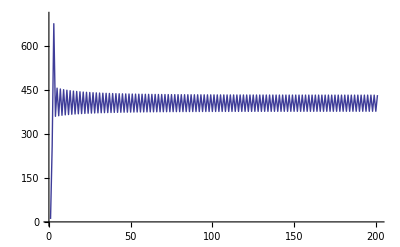

```mathematica
ListPlot[Table[species[28,0.5,0.01,10,t],{t,0,200}],Joined->True,PlotRange->{All,{0,700}}]
```

There is no general solution, as we might expect from the oscillations seen above:

```mathematica
RSolve[n[t+1]==n[t]-d n[t]+b Exp[-a n[t]] n[t],n[t],t]
```

RSolve[n[1+t]==n[t]-d n[t]+b ⅇ^(-a n[t]) n[t],n[t],t]

In reality speciation and extinction are such rare events, that we wouldn't expect the equilibrium ever to be overshot.  This suggests that we should either use small enough time intervals that overshooting does not occur (because b and d are small) or use a continuous-time model.

### Continuous-time approach

dn/dt = - d n[t] + b n[t] Exp[-a n[t]]

```mathematica
Solve[0==-d nhat + b Exp[-a nhat] nhat,nhat]
```

{{nhat→0},{nhat→Log[b/d]/a}}

Here, I've used nhat to stand for the equilibrium.  The first equilibrium to consider is the no-species case.  The second equilibrium is biologically valid only if it is not negative, which requires that b>d.

```mathematica
r=D[-d n[t]+b n[t] Exp[-a n[t]],n[t]]/.n[t]->0
```

b-d

The no-species case will be unstable (r>0), if b>d, that is, if speciation is more common than extinction when there are few species present.

Now considering the second equilibrium:

```mathematica
r=D[-d n[t]+b n[t] Exp[-a n[t]],n[t]]/.n[t]->Log[b/d]/a
```

-d Log[b/d]

As this second equilibrium is only biologically valid when b>d, we know that r must be negative, implying the equilibrium is stable.

Numerical solutions:

```mathematica
species[b_,d_,a_,n0_]:=species[b,d,a,n0]=
NDSolve[{D[n[t],t]==-d n[t]+b Exp[-a n[t]] n[t],n[0]==n0},n[t],{t,0,200}]
```

and plot this solution:

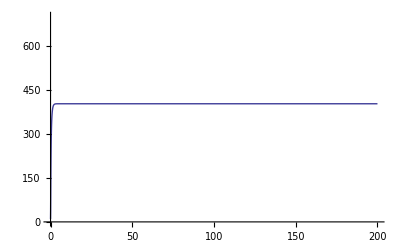

```mathematica
Plot[Evaluate[n[t]/.species[28,0.5,0.01,10]],{t,0,200},PlotRange->{All,{0,700}}]
```

There is no general solution that Mathematica knows:

```mathematica
DSolve[D[n[t],t]==-d n[t]+b Exp[-a n[t]] n[t],n[t],t]
```

{{n[t]→InverseFunction[∫_1^#1 ⅇ^(a K[1])/((-b+d ⅇ^(a K[1])) K[1])ⅆK[1]&][-t+C[1]]}}

## Part 5: Extending to models with more than one variable

The above models were all in one variable (e.g., the population size or the allele frequency).  Fortunately, the ideas are the same (but the methods more cumbersome) with models involving more than one variable.  As an example, let's work with a model of an alternation of generations between haploids and diploids.

Alternation of generations is a life history common to many algae, in which both the haploid and the diploid phases exist as independently growing and reproducing organisms.

Haploid individuals (gametophytes) produce diploid individuals by producing haploid gametes that then unite.

Diploid individuals (sporophytes) produce haploid individuals by meiosis.

During a year, we assume that parents reproduce and then die, where:

	a = the number of diploid offspring produced per haploid parent
	b = the number of haploid offspring produced per diploid parent
	
Then, if h[t] represents the number of haploid individuals and d[t] the number of diploid individuals, we can track the size of both populations over time using discrete-time recursions are thus:

Haploids:  	h[t+1] = b d[t]
Diploids:	d[t+1] = a h[t]

We can describe analogous procedures for continuous-time models, but to keep matters simple , we'll focus here only on discrete-time models

### Equilibria

An equilibrium is defined in the same way, as a special point at which the system stays if started there.  The only trick is to make sure that all of the variables remain constant.

For the model of alternating generations:

```mathematica
Solve[{ĥ ==b d̂,d̂ ==a ĥ},{ĥ,d̂}]
```

{{ĥ→0,d̂→0}}

Here we've asked Mathematica for all of the sets of solutions for the number of haploids and diploids {ĥ,d̂} that cause both of these values to remain constant in the next generation.  The answer is that there's only one equilibrium point, with neither haploids or diploids.

### Stability

To determine stability, we need to have a multi-dimensional analogue of λ that describes the factor by which the distance from the equilibrium grows each generation.

Idea:  We again approximate the recursions near an equilibrium point using the Taylor series, but we do this for each recursion equation and each variable.  For example, if we have two recursion equations, f and g, describing changes in two variables, n and m, we could apply the Taylor series as before and rearrange the results as:

		(n[t+1]-n̂)=(n[t]-n̂) (df/dn)_(n̂,m̂)+(m[t]-m̂) (df/dm)_(n̂,m̂)	
		(m[t+1]-m̂)=(n[t]-n̂) (dg/dn)_(n̂,m̂)+(m[t]-m̂) (dg/dm)_(n̂,m̂)	
  
Book-keeping is easier, however, and we can use the power of matrix algebra, if we write this in matrix form:

		distance to equilibrium in next generation 	= stability matrix times distance to equilibrium in previous generation
		
				(n[t+1]-n̂
m[t+1]-m̂)  		= (df/dn | df/dm
dg/dn | dg/dm) (n[t]-n̂
m[t]-m̂) 
				
But how do we tell if this matrix shrinks the distance or expands the distance?

DEFINITION: A matrix involving d variables has d eigenvalues that describe the factor by which the system grows along different directions (called eigenvectors).  The leading eigenvalue, λ, of a matrix is the largest in magnitude of these eigenvalues, and it predicts whether the matrix stretches (|λ| > 1) or shrinks (|λ| < 1) a vector that it multiplies.  If λ is a complex number, the system will cycle.

CAUTION:  When calculating the stability matrix, decide on an order for the variables and then take the derivative of the recursion for the first variable in the first row with respect to the first variable in the first column.  Keep the order of the variables the same for all subsequent rows and columns.

For example, take the two recursion equations for the haploid-diploid model:

```mathematica
eqnh=b d[t];
eqnd=a h[t];
```

The first equation gives us h[t+1], so we must take the derivatives first with respect to h[t] and then d[t], and then evaluate at the equilibrium of interest (here 0,0):

```mathematica
matrix={{D[eqnh,h[t]],D[eqnh,d[t]]},
{D[eqnd,h[t]],D[eqnd,d[t]]}}/.{h[t]->0,d[t]->0}
```

{{0,b},{a,0}}

The eigenvalues of which are:

```mathematica
Eigenvalues[%]
```

{-√a √b,√a √b}

Because a and b describe the number of offspring, these eigenvalues must be positive.  The magnitude of these two eigenvalues is the same, |λ| = √(a b), which tells us that the system will move away from the equilibrium at {0,0} only if √(a b)>1, which implies that the product of a and b must be greater than one.

	→  A haploid-diploid species can grow in size even if one phase produces less than
	a replacement number of offspring (e.g., a < 1), as long as the other phase compensates (e.g., b > 1).

### Simulation

We can use the same basic code as with the logistic model to track the size of the haploid and diploid populations.  The only difference is that the result is now a vector {h,d}, whose first part is the number of haploids and whose second part is the number of diploids.

```mathematica
hapdip[a_,b_,h0_,d0_,t_]:=hapdip[a,b,h0,d0,t]=
Block[{h=Part[hapdip[a,b,h0,d0,t-1],1],d=Part[hapdip[a,b,h0,d0,t-1],2]},
	{b d, a h}
	]

hapdip[a_,b_,h0_,d0_,0]:={h0,d0}
```

Some notes:  
	* Block keeps a set of calculations together, defining local variables in the first {}.  The output will be the last entry of the Block.
	* := sets the left to the right-hand side only after being called and remembers this value.
	* We have to set a starting point or else the system will end up in an infinite loop going backwards in time.

We can then make a table of population sizes for {haploids, diploids}:

```mathematica
Table[hapdip[0.7,1.5,10,10,t],{t,0,100}]
```

{{10,10},{15.,7.},{10.5,10.5},{15.75,7.35},{11.025,11.025},{16.5375,7.7175},{11.5762,11.5762},{17.3644,8.10337},{12.1551,12.1551},{18.2326,8.50854},{12.7628,12.7628},{19.1442,8.93397},{13.401,13.401},{20.1014,9.38067},{14.071,14.071},{21.1065,9.8497},{14.7746,14.7746},{22.1618,10.3422},{15.5133,15.5133},{23.2699,10.8593},{16.2889,16.2889},{24.4334,11.4023},{17.1034,17.1034},{25.6551,11.9724},{17.9586,17.9586},{26.9378,12.571},{18.8565,18.8565},{28.2847,13.1995},{19.7993,19.7993},{29.699,13.8595},{20.7893,20.7893},{31.1839,14.5525},{21.8287,21.8287},{32.7431,15.2801},{22.9202,22.9202},{34.3803,16.0441},{24.0662,24.0662},{36.0993,16.8463},{25.2695,25.2695},{37.9043,17.6887},{26.533,26.533},{39.7995,18.5731},{27.8596,27.8596},{41.7894,19.5017},{29.2526,29.2526},{43.8789,20.4768},{30.7152,30.7152},{46.0729,21.5007},{32.251,32.251},{48.3765,22.5757},{33.8635,33.8635},{50.7953,23.7045},{35.5567,35.5567},{53.3351,24.8897},{37.3346,37.3346},{56.0018,26.1342},{39.2013,39.2013},{58.8019,27.4409},{41.1614,41.1614},{61.742,28.8129},{43.2194,43.2194},{64.8291,30.2536},{45.3804,45.3804},{68.0706,31.7663},{47.6494,47.6494},{71.4741,33.3546},{50.0319,50.0319},{75.0478,35.0223},{52.5335,52.5335},{78.8002,36.7734},{55.1602,55.1602},{82.7402,38.6121},{57.9182,57.9182},{86.8772,40.5427},{60.8141,60.8141},{91.2211,42.5698},{63.8548,63.8548},{95.7822,44.6983},{67.0475,67.0475},{100.571,46.9333},{70.3999,70.3999},{105.6,49.2799},{73.9199,73.9199},{110.88,51.7439},{77.6159,77.6159},{116.424,54.3311},{81.4967,81.4967},{122.245,57.0477},{85.5715,85.5715},{128.357,59.9001},{89.8501,89.8501},{134.775,62.8951},{94.3426,94.3426},{141.514,66.0398},{99.0597,99.0597},{148.59,69.3418},{104.013,104.013},{156.019,72.8089},{109.213,109.213},{163.82,76.4493},{114.674,114.674}}

or plotting haploids in red and diploids in blue:

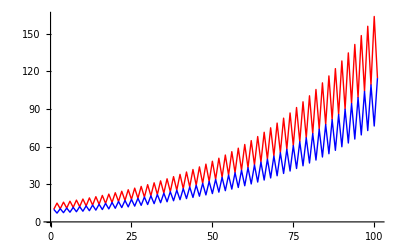

```mathematica
ListPlot[{Table[Part[hapdip[0.7,1.5,10,10,t],1],{t,0,100}],Table[Part[hapdip[0.7,1.5,10,10,t],2],{t,0,100}]},Joined->True,PlotStyle->{Red,Blue}]
```

Notice that in this case the diploids have higher reproductive capacity (1.5 offspring on average), yet it is the haploid population size that grows to a larger size.  This is, of course, because diploids beget haploids.

### A case with complex eigenvalues [EXTRA]

Some systems cycle over time.  As an example, let's consider the classic predator-prey model.

Let H[t] represent the numbers of prey and P[t] represent the numbers of predators.  The prey are assumed to grow exponentially, but they are
captured by predators at a rate that depends on both the availability of prey and predators.

The discrete-time recursions are thus:

Prey:  		H[t+1] = H[t] + r H[t] - b H[t] P[t]
Predator:	P[t+1] = P[t] + c H[t] P[t] - d P[t]

which uses the following parameters:
	the growth rate of the prey in the absence of the predator (r),
	the capture rate at which predators contact and kill prey (b),
	the rate at which eaten prey are turned into predator babies (c),
	and the death rate of predators (d).

The equilibrium of this model is:

```mathematica
Solve[{Ĥ ==Ĥ+r Ĥ-b Ĥ P̂,P̂ ==P̂+c Ĥ P̂-d P̂},{Ĥ,P̂}]
```

{{Ĥ→0,P̂→0},{Ĥ→d/c,P̂→r/b}}

Here we've asked Mathematica for all of the sets of solutions for the number of prey and predators {Ĥ,P̂}that cause both of these values to remain constant in the next generation.

Finding the

```mathematica
eqnH=H[t] + r H[t] - b H[t] P[t];
eqnP= P[t] + c H[t] P[t] - d P[t];
```

```mathematica
matrix={{D[eqnH,H[t]],D[eqnH,P[t]]},
{D[eqnP,H[t]],D[eqnP,P[t]]}}
```

{{1+r-b P[t],-b H[t]},{c P[t],1-d+c H[t]}}

Let's consider the stability of the equilibrium with both prey and predators present:

```mathematica
matrix/.{H[t]->d/c,P[t]->r/b}
```

{{1,-(b d)/c},{(c r)/b,1}}

```mathematica
Eigenvalues[%]
```

{ⅈ (-ⅈ+√d √r),-ⅈ (ⅈ+√d √r)}

where ⅈ=√-1.  The above eigenvalues can be written more simply as {1+ⅈ √(d r),1-ⅈ √(d r)}.  Note that the death rate of predators (d) and the intrinsic growth rate of prey (r) can be assumed to be positive in this model, so these eigenvalues are complex numbers.

Still, the recipe for discrete-time models remains the same:  we find the absolute magnitude of the eigenvalue and if it is greater than one then the system is unstable.  (The rule is slightly different for continuous-time models.  See Chapter 8.)

DEFINITION: The absolute magnitude of a complex number is √((real part)^2+(complex part)^2).

Here, the real part is "1" and the complex part is the part "√(d r)" multiplying ⅈ=√-1.  So the magnitude of both eigenvalues is √((1)^2+(√(d r))^2), or just √(1+d r), which must be a number greater than one.

→  The predator-prey model will cycle (because λ is complex) and expand away 
	from the equilibrium at {H[t]→d/c,P[t]→r/b} (because |λ| > 1).

We can use the same basic code again to track the prey and predator population sizes.

```mathematica
Clear[predprey]
predprey[r_,b_,c_,d_,H0_,P0_,t_]:=predprey[r,b,c,d,H0,P0,t]=
Block[{H=Part[predprey[r,b,c,d,H0,P0,t-1],1],P=Part[predprey[r,b,c,d,H0,P0,t-1],2]},
	{H + r H - b H P, P+ c H P - d P}
	]

predprey[r_,b_,c_,d_,H0_,P0_,0]:={H0,P0}
```

We can then make a table of population sizes for {prey, predators}:

```mathematica
Table[predprey[0.7,0.01,0.0001,0.1,900,70,t],{t,0,100}]
```

{{900,70},{900.,69.3},{906.3,68.607},{918.925,67.9642},{937.633,67.4131},{961.888,66.9927},{990.815,66.7374},{1023.14,66.6761},{1057.15,66.8304},{1090.66,67.2123},{1121.06,67.8216},{1145.48,68.6427},{1161.03,69.6413},{1165.19,70.7628},{1156.31,71.9317},{1133.97,73.0561},{1099.32,74.0348},{1054.96,74.7701},{1004.64,75.181},{952.587,75.2159},{902.901,74.8593},{859.027,74.1324},{823.528,73.0873},{798.103,71.7975},{783.757,70.348},{781.03,68.8267},{790.194,67.3196},{811.373,65.9072},{844.581,64.6641},{889.648,63.659},{946.06,62.9566},{1012.69,62.617},{1087.46,62.6965},{1166.89,63.2448},{1245.71,64.3003},{1316.71,65.8802},{1370.96,67.9667},{1398.83,70.488},{1392.01,73.2993},{1346.08,76.1727},{1262.99,78.8089},{1151.74,80.8815},{1026.41,82.1088},{902.124,82.3256},{790.932,81.5198},{699.818,79.8155},{631.127,77.4196},{584.3,74.5638},{557.634,71.4642},{549.469,68.3029},{558.794,65.2256},{585.473,62.3478},{630.275,59.7633},{694.794,57.5537},{781.27,55.7971},{892.233,54.5767},{1029.84,53.9885},{1194.74,54.1497},{1384.11,55.2042},{1588.9,57.3246},{1790.3,60.7004},{1956.79,65.4976},{2044.89,71.7643},{2008.81,79.2629},{1822.74,87.259},{1508.15,94.4381},{1139.59,99.237},{806.406,100.622},{559.466,98.6743},{399.043,94.3274},{301.967,88.6587},{245.624,82.47},{214.994,76.2487},{201.56,70.2631},{201.03,64.653},{211.779,59.4874},{234.042,54.7985},{269.62,50.6012},{321.923,46.9054},{396.27,43.7248},{500.391,41.085},{645.078,39.0324},{844.844,37.647},{1118.18,37.0629},{1486.47,37.5009},{1969.56,39.3252},{2573.72,43.138},{3265.07,49.9267},{3920.48,61.2355},{4264.09,79.1192},{3875.24,104.944},{2521.06,135.118},{879.388,155.671},{126.011,153.793},{20.4225,140.352},{6.05492,126.603},{2.62765,114.02},{1.47097,102.648},{0.990734,92.3979},{0.768831,83.1672},{0.667597,74.8569}}

or plotting prey in red and predators in blue:

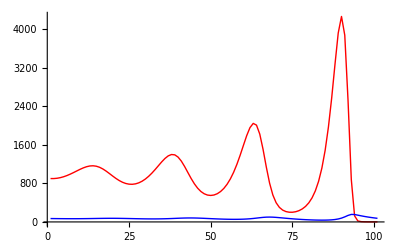

```mathematica
ListPlot[{Table[Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],1],{t,0,100}],Table[Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],2],{t,0,100}]},Joined->True,PlotStyle->{Red,Blue},PlotRange->All]
```

I purposely started this near the equilibrium (1000,70), otherwise it cycles out so fast that it crashes and burns very quickly.  Even here, the prey go extinct by the end of this 100-generation simulation.

I purposely started this near the equilibrium (1000,70), otherwise it cycles out so fast that it crashes and burns very quickly.  Even here, the prey go extinct by the end of this 100-generation simulation.

We can also present this graph as a phase-diagram, where the number of predators (y-axis) is plotted against the number of prey (x-axis):

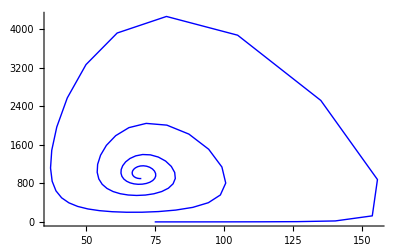

```mathematica
ListPlot[Table[{Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],2],Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],1]},{t,0,100}],Joined->True,PlotStyle->{Red,Blue},PlotRange->All,AxesOrigin->{0,0}]
```

### Accounting for randomness [EXTRA]

In all of the above models, we've assumed that the state of the system can be precisely predicted in the next time step.  Such models are called "deterministic".  In natural systems, there is always a degree of randomness or stochasticity to life.  For example, even if the average number of offspring per parent were 2.3, the actual number will be an integer (0,1,2,3...).   

The offspring number might, for instance, represent a random draw of the Poisson distribution with a certain mean (here 2.3):

```mathematica
RandomInteger[PoissonDistribution[2.3]]
```

0

We can incorporate such randomness (called "demographic stochasticity") into the above ecological models by having the number of offspring be drawn from a Poisson:

```mathematica
Clear[hapdip]
hapdip[a_,b_,h0_,d0_,t_]:=hapdip[a,b,h0,d0,t]=
Block[{h=Part[hapdip[a,b,h0,d0,t-1],1],d=Part[hapdip[a,b,h0,d0,t-1],2]},
numhap=If[b d>0,RandomInteger[PoissonDistribution[b d]],0];
numdip=If[a h >0,RandomInteger[PoissonDistribution[a h]],0];
{numhap,numdip}
	]

hapdip[a_,b_,h0_,d0_,0]:={h0,d0}
```

Some notes:  
	* Block keeps a set of calculations together, defining local variables in the first {}.  The output will be the last entry of the Block.
	* := sets the left to the right-hand side only after being called and remembers this value.
	* We have to set a starting point or else the system will end up in an infinite loop going backwards in time.
	* The Unprotect[...] statements were added so that if the population ever goes extinct, the Poisson distribution can be evaluated even though the mean is zero.  We then know that all draws should return zero, but Mathematica doesn't actually know what to do when the mean is zero by default.  By unprotecting, defining, and reprotecting, we can "force" Mathematica to know something additional.

We can then make a table of population sizes for {haploids, diploids}:

```mathematica
Table[hapdip[0.7,1.5,10,10,t],{t,0,100}]
```

{{10,10},{11,8},{16,14},{18,9},{16,11},{23,10},{17,7},{13,13},{21,7},{6,17},{32,2},{2,16},{21,2},{3,18},{19,2},{3,12},{15,3},{6,11},{14,8},{9,11},{24,8},{6,17},{28,6},{11,16},{21,6},{11,17},{23,7},{10,19},{23,6},{14,19},{41,10},{16,22},{33,8},{8,13},{24,9},{10,18},{36,9},{14,19},{34,9},{11,29},{48,8},{10,37},{63,4},{7,57},{98,3},{4,58},{94,6},{8,64},{98,3},{0,76},{122,0},{0,73},{110,0},{0,72},{101,0},{0,76},{118,0},{0,72},{121,0},{0,77},{118,0},{0,77},{117,0},{0,79},{119,0},{0,93},{131,0},{0,117},{189,0},{0,149},{199,0},{0,136},{208,0},{0,152},{231,0},{0,162},{254,0},{0,184},{278,0},{0,202},{317,0},{0,229},{336,0},{0,248},{346,0},{0,236},{367,0},{0,223},{314,0},{0,226},{335,0},{0,246},{357,0},{0,269},{403,0},{0,280},{421,0},{0,277},{400,0},{0,267},{419,0}}

or plotting haploids in red and diploids in blue:

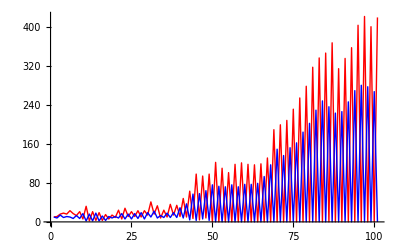

```mathematica
ListPlot[{Table[Part[hapdip[0.7,1.5,10,10,t],1],{t,0,100}],Table[Part[hapdip[0.7,1.5,10,10,t],2],{t,0,100}]},Joined->True,PlotStyle->{Red,Blue}]
```

Reenter this sub-directory a few times to see how the plots change due to demographic stochasticity.  Occassionally, you'll see the whole population go extinct, despite the fact that we expect it to grow with a = 0.7 and b = 1.5.

To learn more about probability theory and stochastic models (both analytical and simulation-based methods), read Primer 3 and Chapters 13-15.

## Part 6: Another example of building a model from scratch

Scenario:  Consider two types of individuals that can help one another to raise a brood (e.g., one type might be better at collecting food “c” and the other type at detecting predators “d”).  Assume that neither of the two types would be able to grow on their own, with the number of offspring per parent, 1-rc and 1-rd, respectively, being less than one.  Through cooperation, however, the per capita growth of each type rises linearly with the number of the other type, with slopes ρc and ρd.

nc[t + 1] = (1 - rc + ρc nd[t]) nc[t]				Discrete - time model
	 nd[t + 1] = (1 - rd + ρd nc[t]) nd[t]

Solving for the equilibrium points that cause nc[t]=nc[t+1] and nd[t]=nd[t+1] simultaneously:
[CAUTION:  When doing this by hand, make sure that you have a solution that solves both of these requirements.]

```mathematica
Solve[{nc==(1-rc+ρc nd) nc,
nd==(1-rd+ρd nc) nd},{nc,nd}]
```

{{nc→rd/ρd,nd→rc/ρc},{nc→0,nd→0}}

Developing the stability matrix:

```mathematica
eqnc=(1-rc+ρc nd[t]) nc[t];
eqnd=(1-rd+ρd nc[t]) nd[t];
```

Using this stability matrix, we replace the numbers of each species, nc[t] and nd[t], with their equilibrium values, first starting with the nc = nd = 0 equilibrium:

```mathematica
matrixEXTINCT={{D[eqnc,nc[t]],D[eqnc,nd[t]]},
{D[eqnd,nc[t]],D[eqnd,nd[t]]}}/.{nc[t]->0,nd[t]->0}
```

{{1-rc,0},{0,1-rd}}

For the {0,0} equilibrium, the eigenvalues are:

```mathematica
Eigenvalues[%]
```

{1-rc,1-rd}

As we've assumed that both 1-rc and 1-rd are less than one, but they represent number of offspring per parent and cannot be negative, both eigenvalues lie between 0 and 1:  this equilibrium is stable.

For the {rc/ρc,rd/ρd} equilibrium, the stability matrix becomes:

```mathematica
matrixPOLY={{D[eqnc,nc[t]],D[eqnc,nd[t]]},
{D[eqnd,nc[t]],D[eqnd,nd[t]]}}/.{nc[t]->rd/ρd,nd[t]->rc/ρc}
```

{{1,(rd ρc)/ρd},{(rc ρd)/ρc,1}}

The eigenvalues of which are:

```mathematica
Eigenvalues[%]
```

{1-√rc √rd,1+√rc √rd}

As we've assumed that both rc and rd are positive, one of these eigenvalues is always greater than one, stretching the system away from {rc/ρc,rd/ρd}.

Simulations:

```mathematica
Clear[coop]
coop[rc_,rd_,ρc_,ρd_,nc0_,nd0_,t_]:=coop[rc,rd,ρc,ρd,nc0,nd0,t]=
Block[{nc=Part[coop[rc,rd,ρc,ρd,nc0,nd0,t-1],1],nd=Part[coop[rc,rd,ρc,ρd,nc0,nd0,t-1],2]},
	{(1-rc+ρc nd) nc,(1-rd+ρd nc) nd}
	]

coop[rc_,rd_,ρc_,ρd_,nc0_,nd0_,0]:={nc0,nd0}
```

For example, consider starting near the equilibrium for the following parameter set:

```mathematica
{nc[t]->rd/ρd,nd[t]->rc/ρc}/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03
```

{nc[t]→10.,nd[t]→30.}

Starting slightly below the equilibrium (collecting species in red and detecting species in blue):

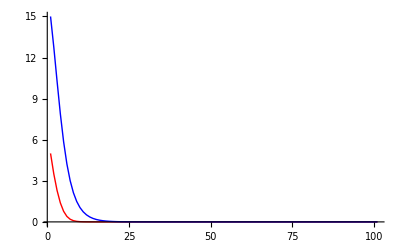

```mathematica
ListPlot[{Table[Part[coop[0.6,0.3,0.02,0.03,5,15,t],1],{t,0,100}],Table[Part[coop[0.6,0.3,0.02,0.03,5,15,t],2],{t,0,100}]},Joined->True,PlotStyle->{Red,Blue},PlotRange->All]
```

Starting one species slight above the equilibrium and the other below (collecting species in red and detecting species in blue):
[THIS IS SENSITIVE TO THE EXACT CHOICES MADE, HERE THERE AREN’T QUITE ENOUGH OF BOTH TO GET THE SYSTEM OFF THE GROUND]

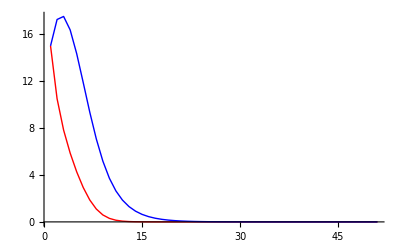

```mathematica
ListPlot[{Table[Part[coop[0.6,0.3,0.02,0.03,15,15,t],1],{t,0,50}],Table[Part[coop[0.6,0.3,0.02,0.03,15,15,t],2],{t,0,50}]},Joined->True,PlotStyle->{Red,Blue},PlotRange->All]
```

Starting slightly above the equilibrium (collecting species in red and detecting species in blue):

```mathematica
ListPlot[{Table[Part[coop[0.6,0.3,0.02,0.03,15,45,t],1],{t,0,50}],Table[Part[coop[0.6,0.3,0.02,0.03,15,45,t],2],{t,0,50}]},Joined->True,PlotStyle->{Red,Blue}]
```

-Graphics-

This system displays a two-species "Allee" effect, where growth cannot occur when either species is rare.  Instead, both species must be reasonably common for there to be enough cooperation present in the system for the populations to take off.

We can also plot vector fields.  How to do this has changed between versions of Mathematica.

If you have version 8, check out:

```mathematica
?VectorPlot
```

VectorPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}] generates a vector plot of the vector field {v_x,v_y} as a function of x and y. 
VectorPlot[{{v_x,v_y},{w_x,w_y},…},{x,x_min,x_max},{y,y_min,y_max}] plots several vector fields.

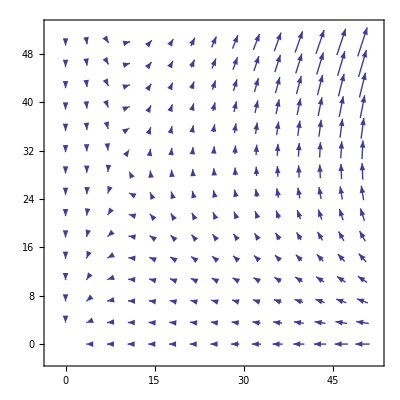

```mathematica
VectorPlot[{(eqnc-nc[t]/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03),(eqnd-nd[t]/.rc->0.1/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03)},{nc[t],0,50},{nd[t],0,50}]
```

```mathematica
?StreamPlot
```

RowBox[{"StreamPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a stream plot of the vector field RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"StreamPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["w", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates plots of several vector fields.

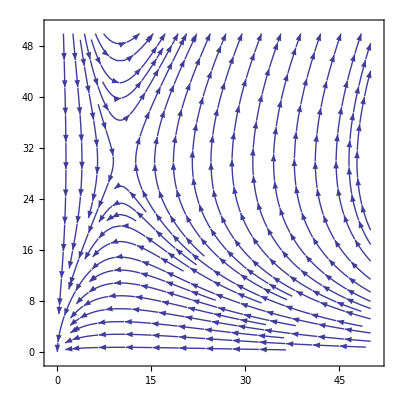

```mathematica
plot2=StreamPlot[{(eqnc-nc[t]/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03),(eqnd-nd[t]/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03)},{nc[t],0,50},{nd[t],0,50}]
```

In versions 6 and 7, we need to load a vector field package:

```mathematica
Needs["VectorFieldPlots`"]
```

```mathematica
?PlotVectorField
```

PlotVectorField[f, {x, x0, x1, (xu)}, {y, y0, y1, (yu)}, (options)] produces a vector field plot of the two-dimensional vector function f.

```mathematica
plot2=PlotVectorField[{(eqnc-nc[t]/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03),(eqnd-nd[t]/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03)},{nc[t],0,400},{nd[t],0,400},Frame->True,ScaleFactor->100,AspectRatio->1,PlotRange->{{-5,410},{-5,410}}]
```

In either version, we can add the equilibria:

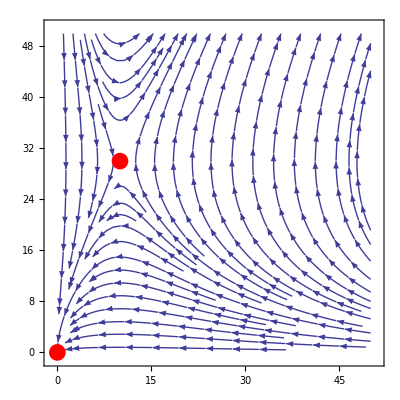

```mathematica
plot3=Show[plot2,
ListPlot[{{0,0},{rd/ρd,rc/ρc}}/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03,PlotStyle->{PointSize[0.03],Red}]
]
```

One might ask how we could separate the domains that are attracted to {0,0} or that grow to infinity.

Some insight is found by dividing the plot regions according to null-clines.  These are lines along which one of the variables remains constant but the other varies.

Specifically, nc will stay constant (but nd can move, i.e., the system can go up or down) along the following line (green in plot below):

```mathematica
Solve[nc==(1-rc+ρc nd) nc,nd]
```

{{nd→rc/ρc}}

Similarly, nd will stay constant (but nc can move, i.e., the system can go left or right) along the following line (purple in plot below):

```mathematica
Solve[nd==(1-rd+ρd nc) nd,nc]
```

{{nc→rd/ρd}}

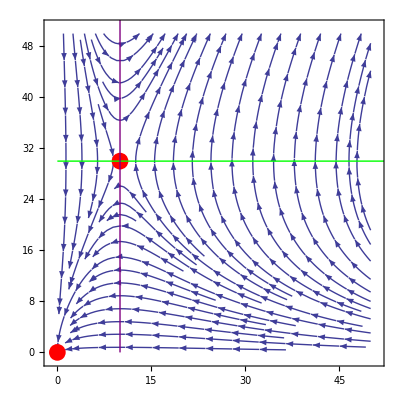

```mathematica
plot4=Show[plot3,
Plot[rc/ρc/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03,{nc[t],0,400},PlotStyle->Green],
ListPlot[{{rd/ρd,0},{rd/ρd,400}}/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03/.ρd->0.001,Joined->True,PlotStyle->Purple]
]
```

In this case, we know that in the top right quadrant, both variables are increasing, so there must be growth of the system.  

Similarly, in the bottom left quadrant, both variables are decreasing, drawing the system toward extinction.

But in the other two quadrants, predictions are off.  For example, in the bottom right, collecting species is decreasing (arrows move left) but detecting species is increasing (arrows move up).  The net result is that the system can either cross the purple line first (doomed to extinction) or the green line (growing indefinitely).

Additional insight can be obtained by finding the eigenvectors along which stretching/shrinking occurs near the equilibrium with both species present:

```mathematica
Eigenvectors[matrixPOLY]
```

{{-(√rd ρc)/(√rc ρd),1},{(√rd ρc)/(√rc ρd),1}}

We can add and subtract these vectors from the equilibrium to draw the eigenvectors (thick grey and black lines):

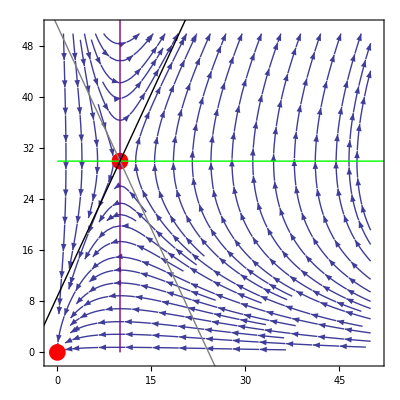

```mathematica
Show[plot4,ListPlot[{{rd/ρd,rc/ρc}-50{-(√rd ρc)/(√rc ρd),1},{rd/ρd,rc/ρc}+50{-(√rd ρc)/(√rc ρd),1}}//.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03,Joined->True,PlotStyle->{Gray,Thick}],
ListPlot[{{rd/ρd,rc/ρc}-50{(√rd ρc)/(√rc ρd),1},{rd/ρd,rc/ρc}+50{(√rd ρc)/(√rc ρd),1}}/.rc->0.6/.rd->0.3/.ρc->0.02/.ρd->0.03,Joined->True,PlotStyle->{Black,Thick}]
]
```

Stretching occurs along the black eigenvector (by a factor given by the eigenvalue 1+√rc √rd}), while shrinking occurs along the gray eigenvector (by a factor given by the eigenvalue 1-√rc √rd}).  So near the equilibrium with both species present, if we start below the gray line, the system is stretched downward eventually, while if we start above the gray line, the system is stretched upward eventually.

These eigenvectors only describe the stretching/shrinking near the equilibrium, however, and it is clear that as we move further from the red equilibrium point, the straight eigenvectors provide a poorer description of where the system eventually heads.

Of course, the above model is just a start.  One limitation is that it predicts that if the populations are able to grow, they do so indefinitely.  In reality, population growth must be limited eventually by competition, but this has not yet been incorporated into the model.

## Appendix: Quick reference to Mathematica

### Getting started

```mathematica
Help -> Documentation Center   - Can be used to search for commands of interest

?Command   - gives a fairly detailed description of a command, e.g., ?Plot tells you all about this command.  
	You can use * as a wildcard, for instance ?*Plot* gives a list of all commands with Plot in their name. 
	More help can be found in the menu under "Help", in the Function Navigator or Documentation Center.
	
*   - Times command (2*3 gives 6).  Spaces can also be used but be careful (e.g, a=2 3 gives six
	but a=23 gives twenty-three)

^   - Power command (2^3 gives 8)

n!  - factorial (3! gives 6)

{}  - denotes a list, e.g., {2,3,4}

()  - Places variables together, e.g., (1+x)/(1-x) takes 1+x over 1-x

[]  - Generally used to denote that something is a function of something else

%# - grabs previous output number #.

%  - grabs the previous line of output regardless of the number

%% - grabs output two lines back.  Note: naming outputs is safer (see next section).

f /. object1 -> object2  
           - tells Mathematica to make replace object1 with object2 in the function
          e.g.,  3*x^2 /. x -> 2*y+z gives  3*(2*y + z)^2
```

### Avoiding conflict with Mathematica

Mathematica tends to use capital letters for its functions, so its often a good idea to use 
lower case names for your functions and variables.

If you refer to previous entries using %, it can be difficult to know exactly what your 
previous entry was.  It is safer to assign a name to the output and then refer to this name later.

For example,

```mathematica
myderivative = D[a Sin[b x], x]
```

```mathematica
Plot[myderivative/.a->1/.b->3,{x,0,10}]
```

### Functions and constants in Mathematica (A small fraction!)

Abs[x]  - Takes the absolute value of x

E   - The exponential constant 2.71838.  E^(x) can be invoked using Exp[x]

I   - The square root of negative 1.

Infinity   - Self-explanatory.

Log[x]   -Takes the natural log of x

Log[b,x]   -Takes the log of x in base b

Pi   - 3.14159...

Sin[x], Cos[x], Tan[x]   - trigonometric functions
ArcSin[x], ArcCos[x], ArcTan[x] -  inverse trigonometric functions

Sqrt[x]   - Square root

### Writing equations in Mathematica

```mathematica
x=y   - Sets x to y immediately and from then on (use Clear[x] to unassign x), e.g., plot1=Plot[x^2,{x,0,10}]

x:=y   - Does nothing until x is called, at which point x is assigned the value y

x==y    - Tests whether x equals y BUT makes no assignment

f[x_]:=  - This is how you define a function (called "f") of x, e.g., f[x_] := x^2

f[x] - This gives the function evaluated at x, e.g., f[3] gives 9 in the above example

f[x_,y_,...]=  - This is how you define a function of several variables
```

### A list of helpful commands

Clear[symbol1,symbol2,...] - clears variable or function definitions, 
	e.g., Clear[x, y, pop1]

Clear[“Global`*”] - clears all variable or function definitions from memory

Collect[eqn,{terms},Factor] - collects parts of an equation involving “terms” and 
	factors them separately (if only one “term”, the braces aren’t needed)
	e.g. Collect[a-b+a x-2 b x+a^2 x^2+2 a b x^2+b^2 x^2, x, Factor]

D[f,x]   - takes the partial derivative of f with respect to x - e.g. D[x^2+y Log[x], x]

D[f, {x, n}]   - takes the nth derivative with respect to x - e.g.  D[x^2+y Log[x],{x,2}]

DSolve[eqn, y[x],x]   - solves differential equation for y as a function of x 
	(SYMBOLICALLY) e.g. DSolve[{y'[x] == k y[x], y[0]==y0, y[x],x]

DSolve[eqns, {y1,y2,y3,..}, x] same as above but for a system of eqns 
	e.g. pred-prey equations DSolve[{y'[x] == k y-x, z'[x]==x+z}, {y[x],z[x]}, x]

NDSolve[eqns, y, {x, xmin,xmax}] - same as DSolve but seeks solution
	NUMERICALLY - e.g. NDSolve[{y'[x] ==4 y[x], y[3]==62}, y[x], {x, 0,20}]

Expand[expr]- expands an expr e.g. Expand[(1+x)^2] gives 1+2x+x^2

Evaluate[object] - evaluates a symbolic object like interpolating functions

Factor[polynomial] - self explanatory - e.g. Factor[x^2 + 2 x + 1]

FindRoot[eqn1==eqn2, {x, x0}] - searches for numerical root of eqn1==eqn2
            starting at x0 e.g. FindRoot[Log[x] + x + Arctan[x] == 0, {x, 4}] tries to find 
            x that satisfies this very ugly - impossible to solve by hand equation, starting at x=4.

For[start,test,increment,body] - repeats procedure “body”, starting from “start”  
	until the “test” condition is met, adding “increment” each time, 
	e.g., For[i=1, i≤10, i=i+1, Print[i]] prints out integers 1 through 10.

Integrate[f,x] - finds indefinite integral of f with respect to x 
	e.g., Integrate[Log[x], x]

Integrate[f, {x, xmin, xmax}] - computes definite integral from xmin to xmax
	e.g., Integrate[Log[x], {x, 1,6}]

ListPlot[list] - plots a list of integers, e.g., ListPlot[{2,4,3,5,4}]

ListPlot[{{x1, y1},{x2, y2},...}] - plots a series of {x, y} values,
	e.g., ListPlot[{{1,2},{2,1},{5,7}}] To join the points with a line use:
	 ListPlot[{{1,2},{2,1},{5,7}},PlotJoined->True] (in Mathematica 5)
	 ListPlot[{{1,2},{2,1},{5,7}},Joined->True] (in more recent versions)

N[f] - gives a numerical value for an expression - e.g. N[Pi] gives 3.14159

Part[eqn,i] - grabs  the ith part of eqn, e.g., Part[3x^2+x^3,2] gives x^3

Plot[f,{x,xmin,xmax}] - plots f versus x on the interval [xmin,xmax] 
            e.g., Plot[x^2, {x,0,2}]   NOTE: Plot has lots of options e.g. AxesLabel,
            Grid, AxesOrigin, etc. See the manual for a complete list and usage 
            e.g.,  Plot[x^2, {x,0,2}, PlotStyle->Dashed] makes a dashed curve.

Plot3D[f, {x, xmin, xmax}, {y, ymin, ymax}] - makes a 3D plot of f

Show[graphics, options] - displays graphic objects using options e.g. 
	Show[popplot1, PlotJoined->True]

Simplify[expr] - does its best to simplify an expression, expr

Solve[eqns, vars] - tries to solve one or a system equations for the vars specified 
	(SYMBOLICALLY)- e.g. Solve[{x+y ==1, x-y ==4}, {x,y}]

NSolve[eqns, vars] - does the same thing as  Solve, but does it NUMERICALLY
	(See also FindRoot)

Sum[f, {i, imin, imax}] - sums  f from i to imax i.e. f[1] + f[2] + f[3] + ... 
            (only really interesting if f depends on i) - e.g. Sum[i, {i, 1,4}] gives 10.
            
Reduce[{eqns}] - can be used to determine if a statement is true or false 
	e.g., Reduce[{a + b > 1, a < 0, b < 0}]
	
RSolve[eqns, vars] - solves a discrete-time equation for y as a function of x 
	(SYMBOLICALLY) e.g. RSolve[{n[t+1] == R n[t], n[0]==n0}, n[t],t]
	
Table[f, {i, imin, imax}]- makes a table in list format of the function f
	with i values that run from imin to imax - e.g. Table[i, {i, 1,4}] gives {1,2,3,4}.

### Libraries

Mathematica has some libraries or packages that it does not load automatically.
The Documentation Center will tell you if a function needs a library.
For example, to plot error bars on a list plot, you will need:

```mathematica
Needs["ErrorBarPlots`"]
```

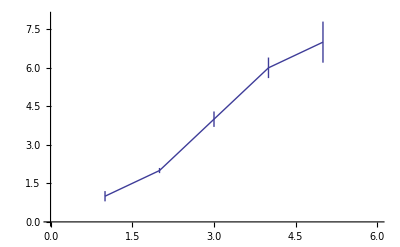

```mathematica
ErrorListPlot[{{{1,1},ErrorBar[0.2]},{{2,2},ErrorBar[0.1]},{{3,4},ErrorBar[0.3]},{{4,6},ErrorBar[0.4]},{{5,7},ErrorBar[0.8]}}, Joined->True,PlotRange->{{0,6},{0,8}}]
```